Kinematics of three-wheeled omnidirectional mobile robot

```mathematica
θ1=π/6; θ2=θ1+(2π)/3;θ3=θ2+(2π)/3;
```

```mathematica
initialPos={0,0,0};
```

```mathematica
R=0.9;
```

```mathematica
wheelDiameter=R; wheelWidth=R/5;
```

```mathematica
wheelPosA={R Cos[θ1],R Sin[θ1],θ1+π/2};
wheelPosB={R Cos[θ2],R Sin[θ2],θ2+π/2};
wheelPosC={R Cos[θ3],R Sin[θ3],θ3+π/2};
```

```mathematica
DrawRobot[{x_,y_,r_}]:={EdgeForm[Black],
Translate[
Rotate[{
Pink,
Disk[{0,0},R],
Black,
Disk[{0,0},R/20],
Gray,
Rotate[Rectangle[{-wheelDiameter/2+wheelPosA[[1]],-wheelWidth/2+wheelPosA[[2]]},{wheelDiameter/2+wheelPosA[[1]],wheelWidth/2+wheelPosA[[2]]}],wheelPosA[[3]]],
Rotate[Rectangle[{-wheelDiameter/2+wheelPosB[[1]],-wheelWidth/2+wheelPosB[[2]]},{wheelDiameter/2+wheelPosB[[1]],wheelWidth/2+wheelPosB[[2]]}],wheelPosB[[3]]],
Rotate[Rectangle[{-wheelDiameter/2+wheelPosC[[1]],-wheelWidth/2+wheelPosC[[2]]},{wheelDiameter/2+wheelPosC[[1]],wheelWidth/2+wheelPosC[[2]]}],wheelPosC[[3]]]

},r,{x,y}],{x,y}]}
```

```mathematica
Graphics[DrawRobot[{0,0,π/12}],Axes->True]
```

-Graphics-

```mathematica
DrawWheelVectors[{x_,y_,r_,vA_,vB_,vC_}]:={EdgeForm[Black],
Translate[
Rotate[{
Blue,
Arrow[{
wheelPosA⟦1;;2⟧,
wheelPosA⟦1;;2⟧+vA {Cos[wheelPosA⟦3⟧],Sin[wheelPosA⟦3⟧]}
}],
Text[Style["vA",Black],(wheelPosA⟦1;;2⟧+ {R/3,R/5})],

Blue,
Arrow[{
wheelPosB⟦1;;2⟧,
wheelPosB⟦1;;2⟧+vB {Cos[wheelPosB⟦3⟧],Sin[wheelPosB⟦3⟧]}
}],
Text[Style["vB",Black],(wheelPosB⟦1;;2⟧+ {-R/3,R/5})],

Blue,
Arrow[{
wheelPosC⟦1;;2⟧,
wheelPosC⟦1;;2⟧+vC {Cos[wheelPosC⟦3⟧],Sin[wheelPosC⟦3⟧]}
}],
Text[Style["vC",Black],(wheelPosC⟦1;;2⟧+ {0,-R/3})],

Blue,Arrow[{{0,0},{R/3,0}}],Text[Style["X",Black],({R/3,0}) 1.5],
Blue,Arrow[{{0,0},{0,R/3}}],Text[Style["Y",Black],({0,R/3}) 1.5]
},r,{x,y}],{x,y}]}
```

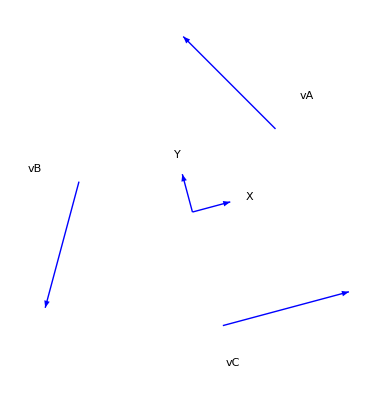

```mathematica
DrawWheelVectors[{0,0,π/12,1,1,1}]//Graphics
```

```mathematica
DrawVelocity[{x_,y_,r_,vx_,vy_}]:={EdgeForm[Black],
Translate[
Rotate[{
Red,
Arrow[{
{0,0},
{0,0}+{vx,vy}
}],
Text[Style["v",Black],( {R/3,R/5})],
},r,{x,y}],{x,y}]}
```

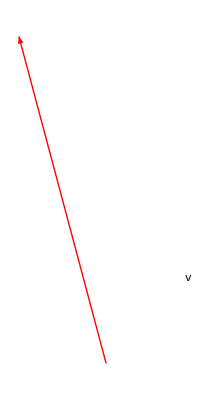

```mathematica
DrawVelocity[{0,0,π/12,0,1}]//Graphics
```

```mathematica
vA=1;vB=1;vC=1;
vWheels={vA,vB,vC};
A=({{-Sin[θ1], Cos[θ1], R}, {-Sin[θ2], Cos[θ2], R}, {-Sin[θ3], Cos[θ3], R}});
```

```mathematica
vRobot={1,0,π/3};
{vA,vB,vC}=A.vRobot
```

{0.442478,0.442478,1.94248}

```mathematica
CalculateVelocities[x_,y_,r_,v_,γ_,ω_]:=Module[{vRobot,vWheels,newpos},
vx=-v Sin[γ];
vy=v Cos[γ];
vRobot={vx,vy}~Join~{ω};
A=({{-Sin[θ1], Cos[θ1], R}, {-Sin[θ2], Cos[θ2], R}, {-Sin[θ3], Cos[θ3], R}});
{vA,vB,vC}=A.vRobot;
vWheels={vA,vB,vC};
show1 = Graphics[DrawRobot[{x,y,r}]];
show2 = Graphics[DrawWheelVectors[{x,y,r,vA,vB,vC}]]; 
show3 = Graphics[DrawVelocity[{x,y,r,vx,vy}]]; 
newpos= {x,y}+RotationMatrix[r,{x,y,1}][[1;;2,1;;2]].{vx,vy}*1.5;
Show[show1,show2,show3,Graphics[Point[newpos]],PlotRange->{{-3,3},{-3,3}},Axes->True]
]
```

```mathematica
Manipulate[CalculateVelocities[x,y,r,velocity,gamma,omega],{x,0,1},{y,0,1},{r,0,2 π},{{velocity,2},0,4},{gamma,0,2π},{omega,0,2},SaveDefinitions->True]
```

```mathematica
A=({{-Sin[θ1], Cos[θ1], R}, {-Sin[θ2], Cos[θ2], R}, {-Sin[θ3], Cos[θ3], R}});
```

```mathematica
(*newvWheels=A.({vx,vy}~Join~{ω});
newpos= {pos[[1]],pos[[2]]}+RotationMatrix[r,{pos[[1]],pos[[2]],1}][[1;;2,1;;2]].{vx,vy} dt;*)
```

```mathematica
SimulateMovement[{pos_,r_,dt_,v_,γ_,ω_,vWheels_}]:=Module[{newpos,newr,newdt,newv,newγ,newω,newvWheels},
vx=-v Sin[γ];
vy=v Cos[γ];
newpos= N[{pos[[1]],pos[[2]]}+RotationMatrix[r,{pos[[1]],pos[[2]],1}][[1;;2,1;;2]].{vx,vy} dt];
newr=r+ω dt;
newdt = dt;
newv = v;
newγ = γ;
newω = ω;
newvWheels=A.({vx,vy}~Join~{ω});
{newpos,newr,newdt,newv,newγ,newω,newvWheels};
Graphics[DrawRobot[newpos~Join~{newr}
]~Join ~
DrawWheelVectors[{newpos[[1]],newpos[[2]],newr,newvWheels⟦1⟧,newvWheels⟦2⟧,newvWheels⟦3⟧}
]~Join~
DrawVelocity[{newpos[[1]],newpos[[2]],newr,-Sin[γ] newv,Cos[γ] newv}]
]]
```

```mathematica
Manipulate[SimulateMovement[{{x,y},r,dt,velocity,gamma,omega,{0,0,0}}],{x,0,1},{y,0,1},{r,0,2 π},{t,0,1,0.1},{{velocity,2},0,4},{gamma,-2 π,2π},{omega,0,2},SaveDefinitions->True]
```

```mathematica
(*intialize*)
steps=20;dt=.1;
pos0={0,0}; r0=0;
v0 = 1; γ0=0;ω0= (2 π)/steps ;vWheels0= {0,0,0};
```

```mathematica
Motion=NestList[SimulateMovement,{pos0,r0,dt,v0,γ0,ω0,vWheels0},steps+1];
%//MatrixForm
```

({0,0} | 0 | 0.1 | 1 | 0 | π/10 | {0,0,0}
{0.,0.1} | 0.0314159 | 0.1 | 1 | 0 | π/10 | {1.14877,-0.583282,0.282743}
{-0.00312549,0.199951} | 0.0628319 | 0.1 | 1 | 0 | π/10 | {1.14877,-0.583282,0.282743}
{-0.00928275,0.299761} | 0.0942478 | 0.1 | 1 | 0 | π/10 | {1.14877,-0.583282,0.282743}
{-0.0182981,0.399354} | 0.125664 | 0.1 | 1 | 0 | π/10 | {1.14877,-0.583282,0.282743}
{-0.0299408,0.498674} | 0.15708 | 0.1 | 1 | 0 | π/10 | {1.14877,-0.583282,0.282743}
{-0.0439499,0.597688} | 0.188496 | 0.1 | 1 | 0 | π/10 | {1.14877,-0.583282,0.282743}
{-0.0600569,0.696382} | 0.219911 | 0.1 | 1 | 0 | π/10 | {1.14877,-0.583282,0.282743}
{-0.0780042,0.794758} | 0.251327 | 0.1 | 1 | 0 | π/10 | {1.14877,-0.583282,0.282743}
{-0.097556,0.892828} | 0.282743 | 0.1 | 1 | 0 | π/10 | {1.14877,-0.583282,0.282743}
{-0.118504,0.99061} | 0.314159 | 0.1 | 1 | 0 | π/10 | {1.14877,-0.583282,0.282743}
{-0.140668,1.08812} | 0.345575 | 0.1 | 1 | 0 | π/10 | {1.14877,-0.583282,0.282743}
{-0.163897,1.18539} | 0.376991 | 0.1 | 1 | 0 | π/10 | {1.14877,-0.583282,0.282743}
{-0.188063,1.28242} | 0.408407 | 0.1 | 1 | 0 | π/10 | {1.14877,-0.583282,0.282743}
{-0.213063,1.37924} | 0.439823 | 0.1 | 1 | 0 | π/10 | {1.14877,-0.583282,0.282743}
{-0.238811,1.47587} | 0.471239 | 0.1 | 1 | 0 | π/10 | {1.14877,-0.583282,0.282743}
{-0.265239,1.57231} | 0.502655 | 0.1 | 1 | 0 | π/10 | {1.14877,-0.583282,0.282743}
{-0.292291,1.66857} | 0.534071 | 0.1 | 1 | 0 | π/10 | {1.14877,-0.583282,0.282743}
{-0.319924,1.76466} | 0.565487 | 0.1 | 1 | 0 | π/10 | {1.14877,-0.583282,0.282743}
{-0.348103,1.86059} | 0.596903 | 0.1 | 1 | 0 | π/10 | {1.14877,-0.583282,0.282743}
{-0.376803,1.95636} | 0.628319 | 0.1 | 1 | 0 | π/10 | {1.14877,-0.583282,0.282743}
{-0.406003,2.05198} | 0.659734 | 0.1 | 1 | 0 | π/10 | {1.14877,-0.583282,0.282743})

```mathematica
ShowResults[{newpos_,newr_,newdt_,newv_,newγ_,newω_,newvWheels_}]:=Graphics[
DrawRobot[newpos~Join~{newr}
]~Join ~
DrawWheelVectors[{newpos[[1]],newpos[[2]],newr,newvWheels⟦1⟧,newvWheels⟦2⟧,newvWheels⟦3⟧}
]~Join~
DrawVelocity[{newpos[[1]],newpos[[2]],newr,-Sin[γ] newv,Cos[γ] newv}],
PlotRange->{{-5,5},{-5,5}},Axes->True,Frame->True
]
```

```mathematica
Anim=Table[ShowResults[Motion[[i]]],{i,1,steps+1}];
```

```mathematica
Manipulate[Evaluate[ShowResults[Motion[[i]]]],
{i,1,steps+1,1},SaveDefinitions->True]
```

Part::pkspec1: The expression i cannot be used as a part specification.

```mathematica
Calculation[{v_,γ_,ω_,pos_,orientation_,dt_,vWheels_}]:=Module[{vx,vy,A,vRobot,newvWheels,newpos,neworientation,newω,newv,newγ},
vx=v Cos[γ];
vy=v Sin[γ];
vRobot={vx,vy}~Join~{ω};
A=({{-Sin[θ1], Cos[θ1], R}, {-Sin[θ2], Cos[θ2], R}, {-Sin[θ3], Cos[θ3], R}});
newvWheels=A.vRobot;
newpos=pos+dt {vx,vy};
neworientation=orientation+ω dt;
newω=ω;
newv=v;
newγ =γ-ω dt;
{newv,newγ,newω,newpos,neworientation,dt,newvWheels}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Drive\MSc\Final-Project\Simulations

```mathematica
(*Export["moving.gif",Anim]*)
```